```mathematica
Quit
```

## Setup:

```mathematica
SetDirectory@NotebookDirectory[];
```

#### Defining the system of equations (autonomous)

```mathematica
z0=6;
n0=-Log[1+z0];
nf=-Log[1];
```

```mathematica
N[n0]
```

-1.94591

```mathematica
xmin=-1;xmax=0.5;
qmin=-0.8;qmax=0.6;
Omin = 0; Omax = 1.1;
```

```mathematica
dx= x'[n]==-(x[n]^2-x[n](2+q[n])-2-2q[n]+3Ω[n]);
dΩ=Ω'[n]==- Ω[n](x[n]+1-2q[n]);
dq=q'[n]==- (j[n]-q[n]-2 q[n]^2);
dj= j'[n]+ (-s[n]-j[n](2+3q[n]))==0;
ds=s'[n]+ (-l[n]-s[n](3+4q[n]))==0;
```

```mathematica
(*Defining RHS only*)
Fx[x_,Ω_,q_]:=-(x^2-x(2+q)-2-2q+3Ω);
FΩ[x_,Ω_,q_]:=-Ω(x+1-2q);
Fq[q_,j_]:=-(j-q-2 q^2);
```

### Models of j:

```mathematica
j0[n_]=1;
j1[n_]=1+3ϵ(1+q[n]);
j2[n_]=1+ϵ;
j3[n_]=1+3ϵ(q[n]-1/2);
```

```mathematica
(*Bella's values*)
qi = -0.647;
ji=1.035;
```

#### Initial values q, j assuming ΛCDM:

```mathematica
HLCDM[z_]:=H0(Ωm0*(1+z)^3+ΩL0)^(1/2)
```

```mathematica
HLCDM'[z]
```

(3 H0 (1+z)^2 Ωm0)/(2 √(ΩL0+(1+z)^3 Ωm0))

```mathematica
qLCDM[z_]=-1+(1+z)HLCDM'[z]/HLCDM[z]//Simplify
```

-1+(3 (1+z)^3 Ωm0)/(2 (ΩL0+(1+z)^3 Ωm0))

```mathematica
jLCDM[z_]=(1+z)/HLCDM[z]^2((1+z)HLCDM'[z]^2 +HLCDM[z]HLCDM'[z]+(1+z)HLCDM[z]HLCDM''[z])-3qLCDM[z]-2//Simplify
```

1

```mathematica
(*Parameter values*)
Ωm0=0.3;
ΩL0=1-Ωm0;
```

```mathematica
(*qi=qLCDM[z0]
ji=jLCDM[z0]*)
```

```mathematica
ϵ0=0
ϵ1=(ji-1)/(3(qi+1))
ϵ2=ji-1
ϵ3=(ji-1)/(3(qi-1/2))
```

0

0.03305

0.035

-0.0101715

```mathematica
qi=0.55;
```

### Initial conditions for specific trajectories

```mathematica
(*ics={{-0.001,0.993243,0.489865},{-0.001,1,0.4},{0.1,0.99,0.4},{0.1,0.99,0.2}};*)
(*x, Ω, q*)
(*ics={{-0.001,0.993243,0.489865}, {-0.001,0.993243,0.52} ,{-0.001,0.993243,0.55} };*)
```

```mathematica
x0a=-10^-3;
Ω0a=0.993243;
```

```mathematica
x0b=-10^-4;
x0c=-10^-2;
```

```mathematica
Ω0b=0.994;
Ω0c=0.995;
```

```mathematica
(*
model 0: q(6)=0.48986486486379105 determined from z(0)=-0.55,
model 1,2,3 q(6) determiend from z(0)=-0.647
q1(6)=0.5370503621671381
q2(6) = 0.4987897437725439
q3(6)= 0.4871436927411515
*)
```

```mathematica
(*q0 determined specifically for each model*)
IC0aa={x0a,Ω0a,0.48986486486379105};
IC1aa={x0a,Ω0a,0.5370503621671381};
IC2aa={x0a,Ω0a,0.4987897437725439};
IC3aa={x0a,Ω0a,0.4871436927411515};
```

```mathematica
IC0ba={x0b,Ω0a,0.48986486486379105};
IC1ba={x0b,Ω0a,0.5370503621671381};
IC2ba={x0b,Ω0a,0.4987897437725439}; 
IC3ba={x0b,Ω0a,0.4871436927411515};
```

```mathematica
(*These are bad*)
IC0ca={x0c,Ω0a,0.48986486486379105};
IC1ca={x0c,Ω0a,0.5370503621671381};
IC2ca={x0c,Ω0a,0.4987897437725439};
IC3ca={x0c,Ω0a,0.4871436927411515};
```

```mathematica
IC0ab={x0a,Ω0b,0.48986486486379105};
IC1ab={x0a,Ω0b,0.5370503621671381};
IC2ab={x0a,Ω0b,0.4987897437725439}; 
IC3ab={x0a,Ω0b,0.4871436927411515};
```

```mathematica
IC0bc={x0b,Ω0c,0.48986486486379105};
IC1bc={x0b,Ω0c,0.5370503621671381};
IC2bc={x0b,Ω0c,0.4987897437725439}; 
IC3bc={x0b,Ω0c,0.4906628069732195};
```

```mathematica
IC0ac={x0a,Ω0c,0.48986486486379105};
IC1ac={x0a,Ω0c,0.5370503621671381};
IC2ac={x0a,Ω0c,0.4987897437725439}; 
IC3ac={x0a,Ω0c,0.4871436927411515};
```

```mathematica
ics0={IC0aa, IC0ba,IC0ab,IC0ac};
ics1={IC1aa, IC1ba,IC1ab,IC1ac};
ics2={IC2aa, IC2ba,IC2ab,IC2ac};
ics3={IC3aa, IC3ba, IC3ab,IC3ac};
```

## Phase space analysis for any j

### Modules

#### Computing s and l

```mathematica
ComputeSL[jFunc_]:=Module[{jPrime,qPrime, qDPrime,sExpr,lExpr},(*Express j and its derivative in terms of q*)
jPrime=D[jFunc,n];
qPrime = Solve[dq,q'[n]][[1,1,2]]/.j[n]->jFunc;
qDPrime = D[qPrime, n];

(*Solve for s and l symbolically*)
sExpr=Solve[dj/. j'[n]->jPrime,s[n]][[1,1,2]]/.q'[n]->qPrime/.j[n]->jFunc//Simplify;

lExpr=Solve[ds,l[n]][[1,1,2]];
lExpr=lExpr/.{s[n]->sExpr,  s'[n]->D[sExpr,n]}/.q'[n]->qPrime/.j[n]->jFunc//Simplify;

Print["s[n] = ",sExpr];
Print["l[n] = ",lExpr];
{sExpr,lExpr}]
```

```mathematica
ComputeSL[j0[n]]//Quiet;
```

s[n] = -2-3 q[n]

l[n] = 9+14 q[n]+6 q[n]^2

```mathematica
ComputeSL[j1[n]]//Quiet;
```

s[n] = -2-9 ϵ-9 ϵ^2-3 (1+4 ϵ+3 ϵ^2) q[n]-3 ϵ q[n]^2

l[n] = 9+48 ϵ+72 ϵ^2+27 ϵ^3+(14+75 ϵ+108 ϵ^2+27 ϵ^3) q[n]+3 (2+9 ϵ+12 ϵ^2) q[n]^2

```mathematica
ComputeSL[j2[n]]//Quiet;
```

s[n] = -((1+ϵ) (2+3 q[n]))

l[n] = (1+ϵ) (9+3 ϵ+14 q[n]+6 q[n]^2)

```mathematica
ComputeSL[j3[n]]//Quiet;
```

s[n] = -2+(9 ϵ^2)/2+(-3+(3 ϵ)/2-9 ϵ^2) q[n]-3 ϵ q[n]^2

l[n] = -3/4 (-12+8 ϵ+3 ϵ^2+18 ϵ^3)+(14+12 ϵ-(27 ϵ^2)/2+27 ϵ^3) q[n]+6 (1+6 ϵ^2) q[n]^2

#### Fixed points and stability module

```mathematica
FixedPointsStability[jExpr_, ϵVal_]:=
Module[{j,fps,Jac,classify,stabilityGrid},
ϵ=ϵVal;
j=jExpr/.q[n]->q;
Print[Fq[x,j]==0];
(*Fixed points*)
(*fps=Solve[{Fx[x,Ω,q]==0,FΩ[x,Ω,q]==0,Fq[q,j]==0}/.ϵ->ϵVal,{x,Ω,q},Reals];*)
fps=NSolve[{Fx[x,Ω,q]==0,FΩ[x,Ω,q]==0,Fq[q,j]==0}/.ϵ->ϵVal,{x,Ω,q},Reals];
Print["=== Fixed Points ==="];
Print[fps//N//TableForm];

(*Jacobian*)
Jac[x_,Ω_,q_]=D[{Fx[x,Ω,q],FΩ[x,Ω,q],Fq[q,j]},{{x,Ω,q}}];

(*Classify each fixed point*)
classify[pt_]:=Module[{vals,eig,type},vals={x,Ω,q}/. pt;
eig=Eigenvalues[Jac@@vals]//N;
type=Which[AllTrue[eig,Re[#]<0&],"Stable node/spiral",AllTrue[eig,Re[#]>0&],"Unstable",True,"Saddle"];
{vals,eig,type}];
stabilityGrid=Grid[Prepend[classify/@fps,{"(x*, Ω*, q*)","Eigenvalues","Type"}],Frame->All];
Print["=== Stability ==="];
Print[stabilityGrid];
Clear[ϵ];
{fps,stabilityGrid}]
```

#### Stream Plot phase space

```mathematica
StreamPlotPhase[jExpr_,ϵVal_]:=
Block[{ϵ=ϵVal,j,vfSliced},
j=jExpr/. {q[n]->q};
vfSliced={Fx[x,1,q],Fq[q,j]};

StreamPlot[vfSliced,{x,xmin,xmax},{q,qmin,qmax},StreamPoints->Fine,Frame->True,FrameLabel->{"x","q"},AspectRatio->1,ImageSize->520,PlotRangePadding->None]]
```

#### Trajectories (q,x)

```mathematica
PhasePortrait[jExpr_,ics_,fps_,ϵVal_]:=Block[{ϵ=ϵVal,SystemEqns,solveIC,sols,trajPlots,colours,labels,fpMarkers,shading,endPoints,startPoints,startPointMarkers,endPointMarkers,domains,qMin,xMin},

SystemEqns={x'[n]==Fx[x[n],Ω[n],q[n]],Ω'[n]==FΩ[x[n],Ω[n],q[n]],q'[n]==Fq[q[n],jExpr/. q[n]->q[n]]};
solveIC[{x0_,Ω0_,q0_}]:=Quiet@NDSolveValue[Join[SystemEqns,{x[n0]==x0,Ω[n0]==Ω0,q[n0]==q0}],{x,Ω,q},{n,n0,nf},Method->"StiffnessSwitching",MaxStepSize->0.0001];
sols=solveIC/@ics;
Print[ics];

colours=ColorData[97]/@Range[Length[ics]];
labels=Map[Row[{"(",ScientificForm[N@#[[1]],2],", ",NumberForm[#[[2]],{4,3}],", ",NumberForm[#[[3]],{4,3}],")"}]&,ics];

trajPlots=MapThread[ParametricPlot[Evaluate[{#1[[1]][n],#1[[3]][n]}],{n,n0,nf},Frame->True,FrameLabel->{"x","q"},PlotStyle->#2]/. Line[pts_]:>{Arrowheads[Join[{0.},ConstantArray[0.04,10]]],#2,Arrow[pts]}&,{sols,colours,labels}];

fpMarkers=Graphics[{PointSize[0.022],Red,Point[{#[[1]],#[[3]]}]&/@N[{x,Ω,q}/. fps]}];
startPoints=Table[{sols[[i,1]][n0],sols[[i,3]][n0]},{i,Length[ics]}];
endPoints=Table[{sols[[i,1]][nf],sols[[i,3]][nf]},{i,Length[ics]}];
endPointMarkers=Graphics[MapThread[{#2,PointSize[0.018],Point[#1],Black,Text[Style[Row[{"(",NumberForm[#1[[1]],{3,2}],", ",NumberForm[#1[[2]],{3,2}],")"}],FontSize->15,FontFamily->"Arial"],#1,{-1.2,1.2}]}&,{endPoints,colours}]];
startPointMarkers=Graphics[MapThread[{#2,PointSize[0.018],Point[#1],Black,Text[Style[Row[{"(",NumberForm[#1[[1]],{3,2}],", ",NumberForm[#1[[2]],{3,2}],")"}],FontSize->15,FontFamily->"Arial"],#1,{-1.2,1.2}]}&,{startPoints,colours}]];
domains=Table[{sols[[i,1]]["Domain"][[1,1]],sols[[i,1]]["Domain"][[1,2]]},{i,Length[ics]}];
qMin=Min[Table[NMinValue[{sols[[i,3]][n],domains[[i,1]]<=n<=domains[[i,2]]},n],{i,Length[ics]}]];
xMin=Min[Table[NMinValue[{sols[[i,1]][n],domains[[i,1]]<=n<=domains[[i,2]]},n],{i,Length[ics]}]];
j=jExpr/. q[n]->q;
Print["The viable regions are: \n",Reduce[(x/(j-q-2)>=0),x]];

shading=RegionPlot[(x/(j-q-2)>=0)&&(q>-1),{x,-3,0.5},{q,qMin-0.5,qmax},PlotStyle->RGBColor[0.5,0.5,1,0.2],BoundaryStyle->None,Frame->False,PlotPoints->80];
Print[StringJoin["(x0, q0) =",ToString[endPoints]]];

(*── CHANGED:Legended[Show[...],...] instead of PlotLegends inside Show ──*)
Legended[Show[trajPlots,shading,endPointMarkers,startPointMarkers,PlotRange->{{xmin,xmax},{qmin,qmax}},AspectRatio->1,ImageSize->500,PlotRangePadding->None],Placed[LineLegend[colours,labels,LegendLabel->Style["(x_0, Ω_0, q_0)",11,Italic]],{Left,Top}]]]
```

#### Trajectories (x, Omega)

```mathematica
PhasePortraitxΩ[jExpr_,ics_,fps_,ϵVal_]:=Block[{ϵ=ϵVal,SystemEqns,solveIC,sols,trajPlots,colours,labels,fpMarkers,shading,endPoints,startPoints,startPointMarkers,endPointMarkers,domains,OMin,xMin},SystemEqns={x'[n]==Fx[x[n],Ω[n],q[n]],Ω'[n]==FΩ[x[n],Ω[n],q[n]],q'[n]==Fq[q[n],jExpr/. q[n]->q[n]]};
solveIC[{x0_,Ω0_,q0_}]:=Quiet@NDSolveValue[Join[SystemEqns,{x[n0]==x0,Ω[n0]==Ω0,q[n0]==q0}],{x,Ω,q},{n,n0,nf},Method->"StiffnessSwitching",MaxStepSize->0.0001];
sols=solveIC/@ics;
Print[ics];
(*colours and labels*)colours=ColorData[97]/@Range[Length[ics]];
labels=Map[Row[{"(",ScientificForm[N@#[[1]],2],", ",NumberForm[#[[2]],{4,3}],", ",NumberForm[#[[3]],{4,3}],")"}]&,ics];
trajPlots=MapThread[ParametricPlot[Evaluate[{#1[[1]][n],#1[[2]][n]}],{n,n0,nf},Frame->True,FrameLabel->{"x","Ω"},PlotStyle->#2,PlotRange->All]/. Line[pts_]:>{Arrowheads[Join[{0.},ConstantArray[0.04,10]]],#2,Arrow[pts]}&,{sols,colours,labels}];
fpMarkers=Graphics[{PointSize[0.022],Red,Point[{#[[1]],#[[2]]}]&/@N[{x,Ω,q}/. fps]}];
startPoints=Table[{sols[[i,1]][n0],sols[[i,2]][n0]},{i,Length[ics]}];
endPoints=Table[{sols[[i,1]][nf],sols[[i,2]][nf]},{i,Length[ics]}];
endPointMarkers=Graphics[MapThread[{#2,PointSize[0.018],Point[#1],Black,FontSize->11,Text[Style[Row[{"(",NumberForm[#1[[1]],{3,2}],", ",NumberForm[#1[[2]],{3,2}],")"}],FontSize->15,FontFamily->"Arial"],#1,{-1.2,1.2}]  (*offset:adjust {-1.2,1.2} to reposition labels*)}&,{endPoints,colours}]];
startPointMarkers=Graphics[MapThread[{#2,PointSize[0.018],Point[#1],Black,FontSize->11,Text[Style[Row[{"(",NumberForm[#1[[1]],{3,2}],", ",NumberForm[#1[[2]],{3,2}],")"}],FontSize->15,FontFamily->"Arial"],#1,{-1.2,1.2}]}&,{startPoints,colours}]];
(*Get the actual domain of each solution (may stop early due to WhenEvent)*)domains=Table[{sols[[i,1]]["Domain"][[1,1]],sols[[i,1]]["Domain"][[1,2]]},{i,Length[ics]}];
(*Sample q over each trajectory's domain and find global min/max*)OMin=Min[Table[NMinValue[{sols[[i,2]][n],domains[[i,1]]<=n<=domains[[i,2]]},n],{i,Length[ics]}]];
xMin=Min[Table[NMinValue[{sols[[i,1]][n],domains[[i,1]]<=n<=domains[[i,2]]},n],{i,Length[ics]}]];
(*Viable region:x/(j(q)-q-2)>=0,restricted to q>-1*)j=jExpr/. q[n]->q;

Legended[Show[trajPlots,endPointMarkers,startPointMarkers,PlotRange->{{xmin,xmax},{Omin,Omax}},AspectRatio->1,ImageSize->500,PlotRangePadding->None],Placed[LineLegend[colours,labels,LegendLabel->Style["(x_0, Ω_0, q_0)",11,Italic]],{Left,Top}]]]
```

### Model 0 analysis

#### Computing s and l:

```mathematica
ComputeSL[j0[n]]//Quiet;
```

s[n] = -2-3 q[n]

l[n] = 9+14 q[n]+6 q[n]^2

#### Fixed points and stability:

```mathematica
{fps0,stability0}=FixedPointsStability[j0[n],ϵ0];
```

-1+x+2 x^2==0

=== Fixed Points ===

q→-1. | x→-3. | Ω→-4.
q→-1. | x→1. | Ω→0.
q→-1. | x→0. | Ω→0.
q→0.5 | x→3.386 | Ω→0.
q→0.5 | x→0. | Ω→1.
q→0.5 | x→-0.886001 | Ω→0.

=== Stability ===

(x*, Ω*, q*) | Eigenvalues | Type
{-3.,-4.,-1.} | {4.,-3.,3.} | Saddle
{1.,0.,-1.} | {-4.,-3.,-1.} | Stable node/spiral
{0.,0.,-1.} | {-3.,-3.,1.} | Saddle
{3.386,0.,0.5} | {-4.272,-3.386,3.} | Saddle
{0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
{-0.886001,0.,0.5} | {4.272,3.,0.886001} | Unstable

```mathematica
(*Table using Solve
{{"(x*, Ω*, q*)", "Eigenvalues", "Type"}, {{-3,-4,-1}, {4.,-3.,3.}, "Saddle"}, {{0,0,-1}, {-3.,-3.,1.}, "Saddle"}, {{0,1,1/2}, {3.3860009363293826,3.,-0.8860009363293826}, "Saddle"}, {{1,0,-1}, {-4.,-3.,-1.}, "Stable node/spiral"}, {{1/4 (5-√73),1/3 (3+5/8 (5-√73)-1/16 (5-√73)^2),1/2}, {4.272001872658765,3.,0.8860009363293826}, "Unstable"}, {{1/4 (5+√73),1/3 (3+5/8 (5+√73)-1/16 (5+√73)^2),1/2}, {-4.272001872658765,-3.3860009363293826,3.}, "Saddle"}}*)
```

#### Stream phase plot:

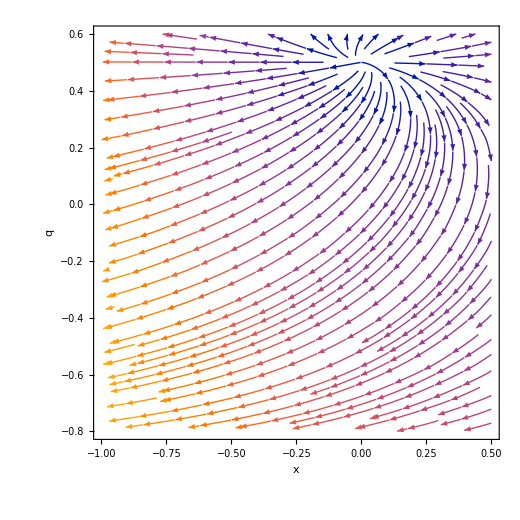

```mathematica
stream0=StreamPlotPhase[j0[n], ϵ0]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/Model 0/PhasePortrait.png",stream0];
```

#### Phase portrait with trajectories

{{-1/1000,0.993243,0.489865},{-1/10000,0.993243,0.489865},{-1/1000,0.994,0.489865},{-1/1000,0.995,0.489865}}

The viable regions are: 
(q<-1&&x≥0)||(q>-1&&x≤0)

(x0, q0) ={{-0.271093, -0.55}, {-0.0245374, -0.55}, {-0.489434, -0.55}, {-0.839323, -0.55}}

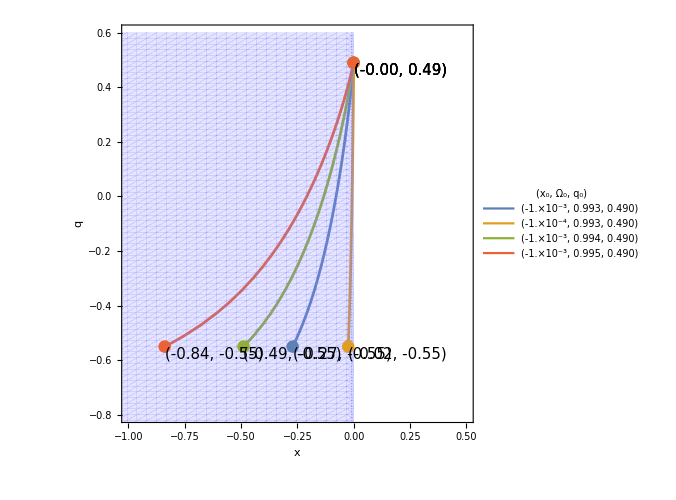

```mathematica
portrait0=PhasePortrait[j0[n],ics0,fps0, ϵ0]
SaveName=StringJoin["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/Model 0/PhasePlaneTraj.png"];
Export[SaveName,portrait0];
```

{{-1/1000,0.993243,0.489865},{-1/10000,0.993243,0.489865},{-1/1000,0.994,0.489865},{-1/1000,0.995,0.489865}}

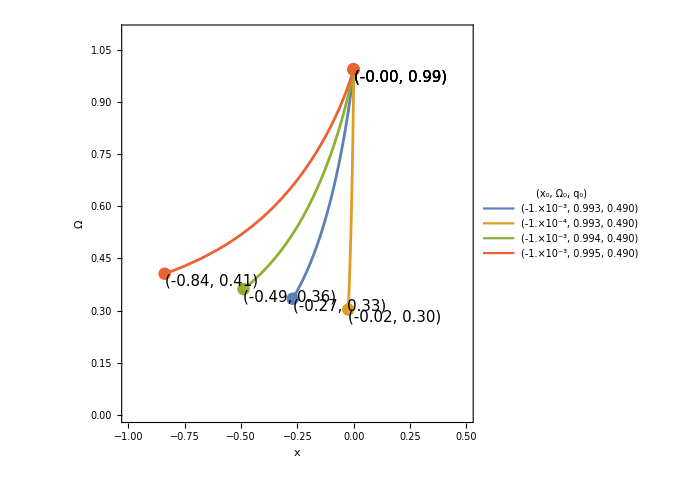

```mathematica
portrait0xΩ=PhasePortraitxΩ[j0[n],ics0,fps0, ϵ0]
SaveName=StringJoin["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/Model 0/PhasePlaneTraj_xO.png"];
Export[SaveName,portrait0xΩ];
```

### Model 1 analysis

#### Computing s and l:

```mathematica
ComputeSL[j1[n]]//Quiet;
```

s[n] = -2-3 ϵ+9 ϵ^2+3 (-1-6 ϵ+3 ϵ^2) q[n]-15 ϵ q[n]^2

l[n] = 9 (1+4 ϵ+2 ϵ^2-3 ϵ^3)+(14+87 ϵ+90 ϵ^2-27 ϵ^3) q[n]+(6+51 ϵ+72 ϵ^2) q[n]^2

#### Fixed points and stability:

```mathematica
{fps1,stability1}=FixedPointsStability[j1[n],ϵ1];
```

-1-0.0991501 (1+q)+x+2 x^2==0

=== Fixed Points ===

q→-1. | x→-3. | Ω→-4.
q→-1. | x→1. | Ω→0.
q→-1. | x→0. | Ω→0.
q→0.549575 | x→3.44832 | Ω→0.
q→0.549575 | x→0.0991501 | Ω→1.11404
q→0.549575 | x→-0.898743 | Ω→0.

=== Stability ===

(x*, Ω*, q*) | Eigenvalues | Type
{-3.,-4.,-1.} | {4.,-3.,3.} | Saddle
{1.,0.,-1.} | {-4.,-3.,-1.} | Stable node/spiral
{0.,0.,-1.} | {-3.,-3.,1.} | Saddle
{3.44832,0.,0.549575} | {-4.34706,-3.34917,3.1983} | Saddle
{0.0991501,1.11404,0.549575} | {3.34917,3.1983,-0.997893} | Saddle
{-0.898743,0.,0.549575} | {4.34706,3.1983,0.997893} | Unstable

#### Stream phase plot:

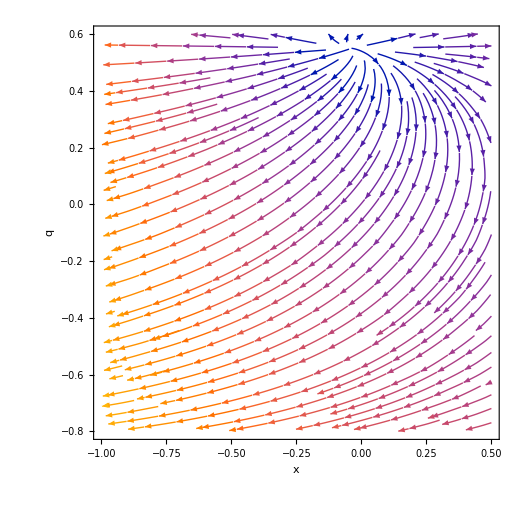

```mathematica
stream1=StreamPlotPhase[j1[n], ϵ1]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/Model 1/PhasePortrait.png",stream1];
```

#### Phase portrait with trajectories

{{-1/1000,0.993243,0.53705},{-1/10000,0.993243,0.53705},{-1/1000,0.994,0.53705},{-1/1000,0.995,0.53705}}

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

The viable regions are: 
(q<-1.&&x≥0)||(q>-1.&&x≤0)

(x0, q0) ={{0.224965, -0.647}, {0.369294, -0.647}, {0.101242, -0.647}, {-0.0870811, -0.647}}

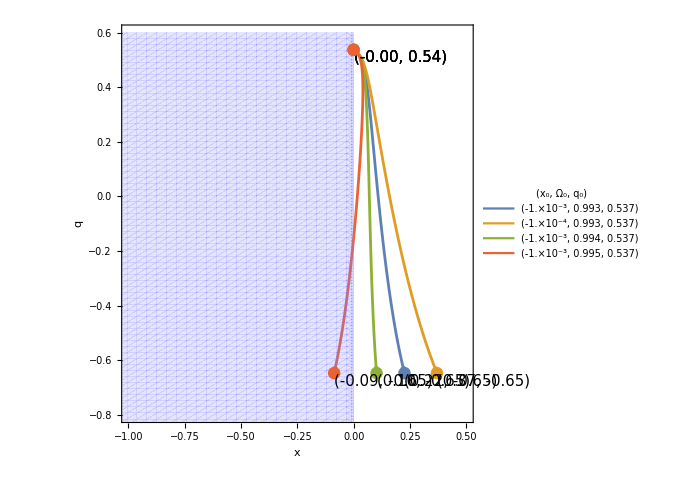

```mathematica
portrait1=PhasePortrait[j1[n],ics1,fps1, ϵ1]
SaveName=StringJoin["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/Model 1/PhasePlaneTraj.png"];
Export[SaveName,portrait1];
```

{{-1/1000,0.993243,0.53705},{-1/10000,0.993243,0.53705},{-1/1000,0.994,0.53705},{-1/1000,0.995,0.53705}}

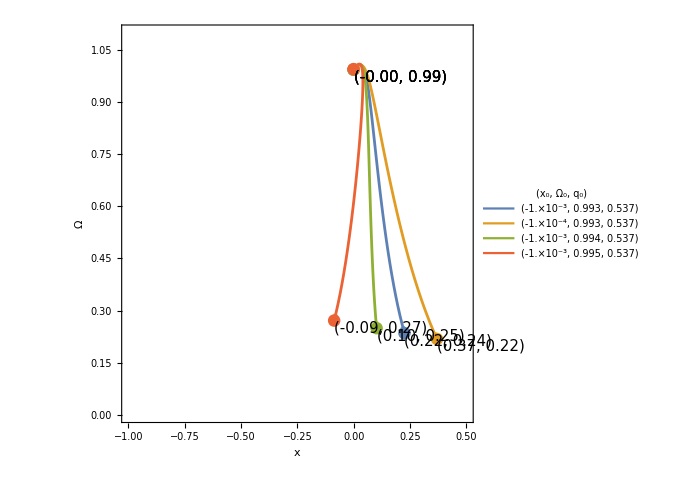

```mathematica
portrait1xΩ=PhasePortraitxΩ[j1[n],ics1,fps1, ϵ1]
SaveName=StringJoin["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/Model 1/PhasePlaneTraj_xO.png"];
Export[SaveName,portrait1xΩ];
```

### Model 2 analysis

```mathematica
j2[n]
```

1+ϵ

#### Computing s and l:

```mathematica
ComputeSL[j2[n]]//Quiet;
```

s[n] = -((1+ϵ) (2+3 q[n]))

l[n] = (1+ϵ) (9+3 ϵ+14 q[n]+6 q[n]^2)

#### Fixed points and stability:

```mathematica
{fps2,stability2}=FixedPointsStability[j2[n],ϵ2];
```

-1.035+x+2 x^2==0

=== Fixed Points ===

q→-1.01158 | x→-3.02315 | Ω→-4.05026
q→-1.01158 | x→0.964414 | Ω→0.
q→-1.01158 | x→0.024009 | Ω→0.
q→0.511577 | x→3.40059 | Ω→0.
q→0.511577 | x→0.0231546 | Ω→1.02692
q→0.511577 | x→-0.88901 | Ω→0.

=== Stability ===

(x*, Ω*, q*) | Eigenvalues | Type
{-3.02315,-4.05026,-1.01158} | {3.98757,3.04716,-3.04631} | Saddle
{0.964414,0.,-1.01158} | {-3.98757,-3.04631,-0.940405} | Stable node/spiral
{0.024009,0.,-1.01158} | {-3.04716,-3.04631,0.940405} | Saddle
{3.40059,0.,0.511577} | {-4.2896,-3.37743,3.04631} | Saddle
{0.0231546,1.02692,0.511577} | {3.37743,3.04631,-0.912164} | Saddle
{-0.88901,0.,0.511577} | {4.2896,3.04631,0.912164} | Unstable

#### Stream phase plot:

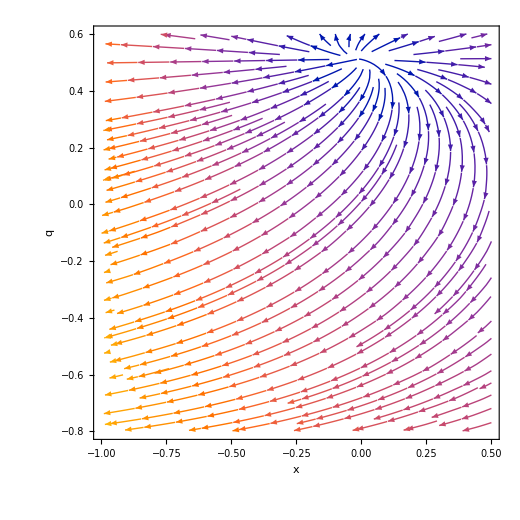

```mathematica
stream2=StreamPlotPhase[j2[n], ϵ2]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/Model 2/PhasePortrait.png",stream2];
```

#### Phase portrait with trajectories

{{-1/1000,0.993243,0.49879},{-1/10000,0.993243,0.49879},{-1/1000,0.994,0.49879},{-1/1000,0.995,0.49879}}

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

The viable regions are: 
(q<-0.965&&x≥0)||(q>-0.965&&x≤0)

(x0, q0) ={{-0.473308, -0.647}, {-0.223593, -0.647}, {-0.694099, -0.647}, {-1.04681, -0.647}}

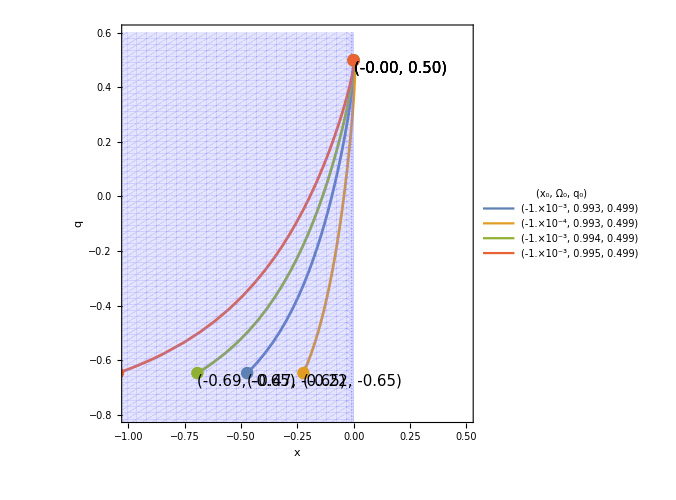

```mathematica
portrait2=PhasePortrait[j2[n],ics2,fps2, ϵ2]
SaveName=StringJoin["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/Model 2/PhasePlaneTraj.png"];
Export[SaveName,portrait2];
```

{{-1/1000,0.993243,0.49879},{-1/10000,0.993243,0.49879},{-1/1000,0.994,0.49879},{-1/1000,0.995,0.49879}}

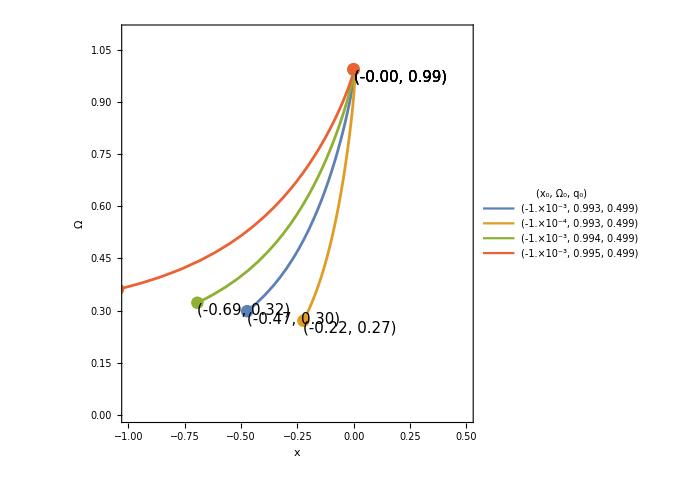

```mathematica
portrait2xΩ=PhasePortraitxΩ[j2[n],ics2,fps2, ϵ2]
SaveName=StringJoin["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/Model 2/PhasePlaneTraj_xO.png"];
Export[SaveName,portrait2xΩ];
```

### Model 3 analysis

```mathematica
j3[z]
```

1+3 ϵ (-1/2+q[z])

```mathematica
ϵ3
```

-0.0101715

#### Computing s and l:

```mathematica
ComputeSL[j3[n]]//Quiet;
```

s[n] = -1/2 (2-3 ϵ)^2+(-3-(9 ϵ)/2+9 ϵ^2) q[n]-15 ϵ q[n]^2

l[n] = 9/4 (4-8 ϵ-ϵ^2+6 ϵ^3)+(14+24 ϵ-(63 ϵ^2)/2-27 ϵ^3) q[n]+6 (1+4 ϵ+12 ϵ^2) q[n]^2

#### Fixed points and stability:

```mathematica
{fps3,stability3}=FixedPointsStability[j3[n],ϵ3];
```

-1+0.0305144 (-1/2+q)+x+2 x^2==0

=== Fixed Points ===

q→-1.01526 | x→-3.03051 | Ω→-4.06627
q→-1.01526 | x→0.952714 | Ω→0.
q→-1.01526 | x→0.0320289 | Ω→0.
q→0.5 | x→3.386 | Ω→0.
q→0.5 | x→0. | Ω→1.
q→0.5 | x→-0.886001 | Ω→0.

=== Stability ===

(x*, Ω*, q*) | Eigenvalues | Type
{-3.03051,-4.06627,-1.01526} | {3.98323,3.06254,-3.06103} | Saddle
{0.952714,0.,-1.01526} | {-3.98323,-3.06103,-0.920685} | Stable node/spiral
{0.0320289,0.,-1.01526} | {-3.06254,-3.06103,0.920685} | Saddle
{3.386,0.,0.5} | {-4.272,-3.386,3.} | Saddle
{0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
{-0.886001,0.,0.5} | {4.272,3.,0.886001} | Unstable

#### Stream phase plot:

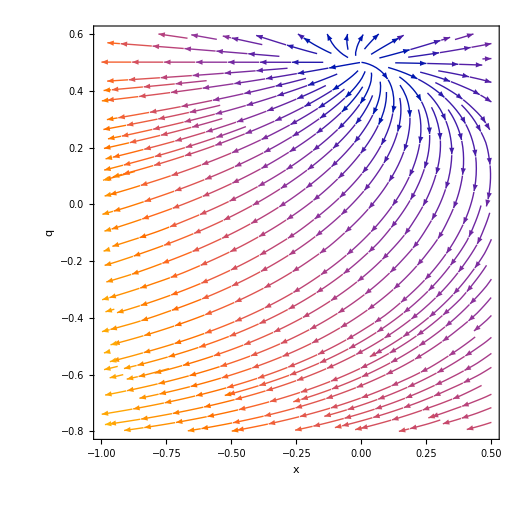

```mathematica
stream3=StreamPlotPhase[j3[n], ϵ3]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/Model 3/PhasePortrait.png",stream3];
```

#### Phase portrait with trajectories

{{-1/1000,0.993243,0.487144},{-1/10000,0.993243,0.487144},{-1/1000,0.994,0.487144},{-1/1000,0.995,0.487144}}

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

The viable regions are: 
(q<-0.955584&&x≥0)||(q>-0.955584&&x≤0)

(x0, q0) ={{-0.811435, -0.647}, {-0.501177, -0.647}, {-1.09043, -0.647}, {-1.54713, -0.647}}

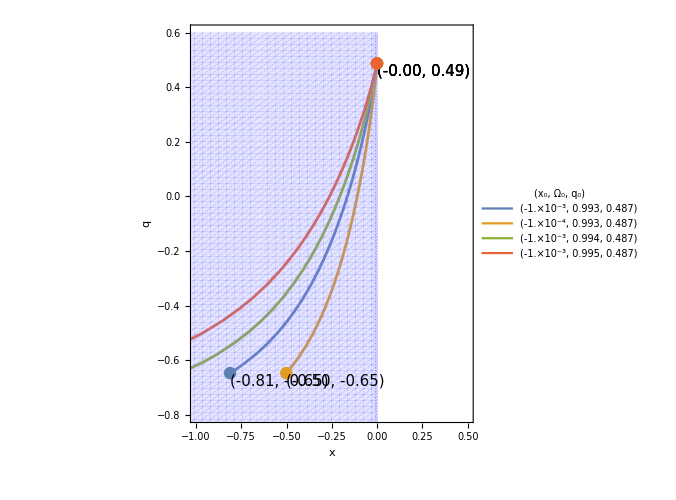

```mathematica
portrait3=PhasePortrait[j3[n],ics3,fps3, ϵ3]
SaveName=StringJoin["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/Model 3/PhasePlaneTraj.png"];
Export[SaveName,portrait3];
```

{{-1/1000,0.993243,0.487144},{-1/10000,0.993243,0.487144},{-1/1000,0.994,0.487144},{-1/1000,0.995,0.487144}}

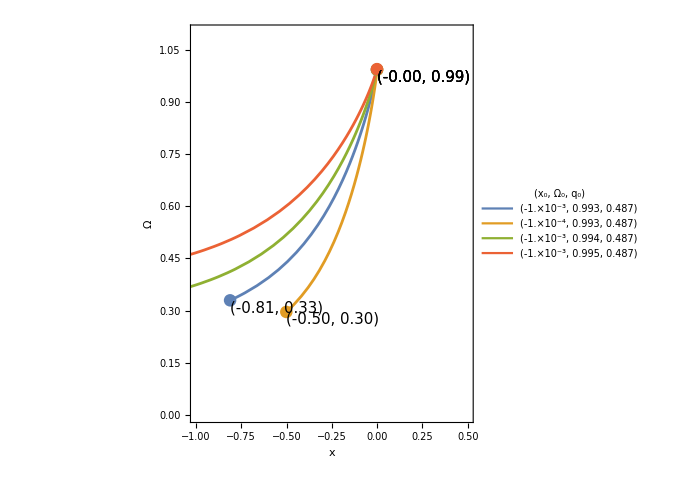

```mathematica
portrait3xΩ=PhasePortraitxΩ[j3[n],ics3,fps3, ϵ3]
SaveName=StringJoin["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/Model 3/PhasePlaneTraj_xO.png"];
Export[SaveName,portrait3xΩ];
```